## NURBS Curve

```mathematica
Table[Random[],{i,10}]
```

{0.065875,0.783911,0.262234,0.563481,0.702404,0.424803,0.497298,0.157523,0.703686,0.081724}

## BSpline Surface

```mathematica
surfKnots={0,0,0,0,.5,1,1,1,1};
cpts={{{1,1,-0.7417486553512296},{1,2,-0.8272445659579368},{1,3,0.056384039811391506},{1,4,-0.8565668867842464},{1,5,-0.027038808836199912}},{{2,1,-0.8954639917925951},{2,2,0.7766849857222553},{2,3,-0.2762882340944248},{2,4,0.18616037830975074},{2,5,-0.8933549711042139}},{{3,1,-0.4470460035460979},{3,2,-0.9258719097096733},{3,3,-0.5237670863586921},{3,4,0.11854173291263326},{3,5,0.9615924014809489}},{{4,1,0.9195532263713426},{4,2,-0.10327619833646784},{4,3,-0.16756710093868232},{4,4,0.7063963753875271},{4,5,-0.05516995763136112}},{{5,1,0.9561682326127552},{5,2,-0.500642765940114},{5,3,0.2473747081580262},{5,4,0.10467945795748923},{5,5,0.5112014481491505}}};
ToExpression[Import["/tmp/bspline_surf.txt","String"]];
surfpts=surf[[All,1;;3]];
surfU=(Arrow[{{#1,#2,#3},{#1,#2,#3}+{#4,#5,#6}/25}])&@@@surf;
surfV=(Arrow[{{#1,#2,#3},{#1,#2,#3}+{#7,#8,#9}/25}])&@@@surf;
b=Graphics3D[BSplineSurface[cpts,SplineDegree->3,SplineKnots->{surfKnots,surfKnots}]];
Show[Graphics3D[{
PointSize[Medium],Blue,Point[surfpts],
Gray,Line[cpts],Line[Transpose[cpts]],
Arrowheads[Small],Green,surfU,
Arrowheads[Small],Red,surfV,
}],b]
```

-Graphics3D-

```mathematica
surfU[[1]]
```

## BSpline Basis

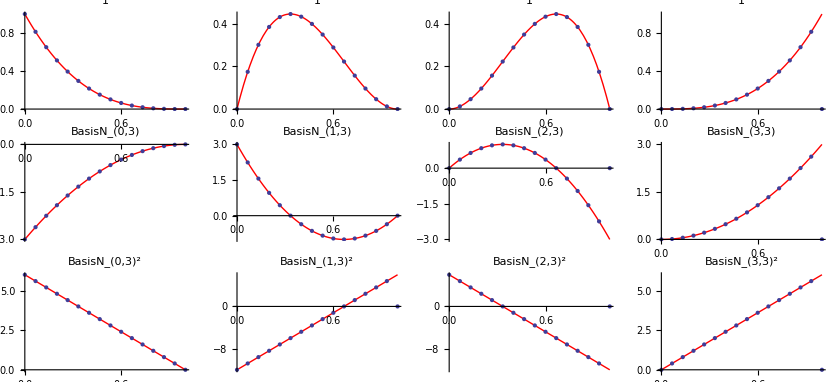

```mathematica
ToExpression[Import["/tmp/bspline_basis.txt","String"]]
GraphicsGrid[Table[Table[
Show[{
Plot[
D[BSplineBasis[{p,knots},i,x],{x,k}]/.x->xx,{xx,knots[[1]],knots[[numKnots-p]]},
PlotStyle->Red,
PlotLabel->Subscript[BasisN, i,p]^(k) ,
PlotRange->Full],
ListPlot[nn[i,p,k]]
}] 
,{i,0,numKnots-p-2}],{k,0,2}]
]
```

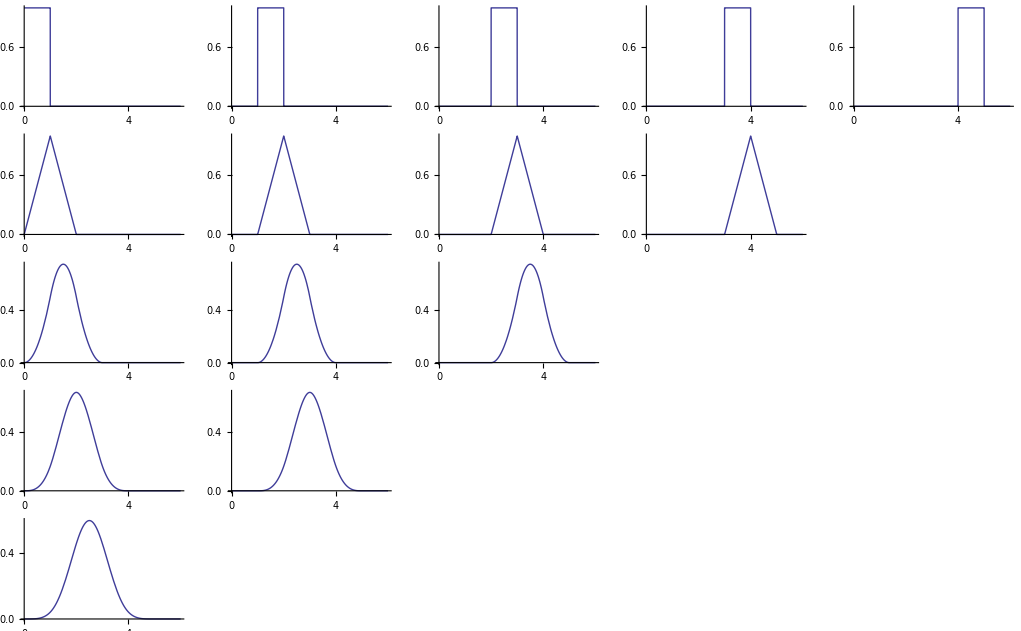

```mathematica
opp=5; knots=Table[i-1,{i,opp+1}];
GraphicsGrid[Table[Table[
Plot[BSplineBasis[{d,knots},i,x],{x,0,opp+1}]
,{i,0,opp-d-1}],{d,0,opp-1}]]
```